# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2021-12-25

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Virginia,Washington,Washington DC,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-11,88},{2021-12-12,49},{2021-12-13,165},{2021-12-14,192},{2021-12-15,119},{2021-12-16,138},{2021-12-17,147},{2021-12-18,120},{2021-12-19,67},{2021-12-20,185},{2021-12-21,206},{2021-12-22,87},{2021-12-23,5},{2021-12-24,3},{2021-12-25,9}},California→{{2021-12-11,589},{2021-12-12,231},{2021-12-13,1066},{2021-12-14,985},{2021-12-15,1336},{2021-12-16,1314},{2021-12-17,1427},{2021-12-18,1219},{2021-12-19,445},{2021-12-20,1123},{2021-12-21,3212},{2021-12-22,3461},{2021-12-23,51},{2021-12-24,9},{2021-12-25,13}},Colorado→{{2021-12-11,186},{2021-12-12,283},{2021-12-13,256},{2021-12-14,411},{2021-12-15,479},{2021-12-16,486},{2021-12-17,463},{2021-12-18,450},{2021-12-19,49},{2021-12-20,458},{2021-12-21,379},{2021-12-22,157},{2021-12-23,143},{2021-12-24,95},{2021-12-25,51}},Connecticut→{{2021-12-11,113},{2021-12-12,56},{2021-12-13,161},{2021-12-14,181},{2021-12-15,159},{2021-12-16,164},{2021-12-17,164},{2021-12-18,86},{2021-12-19,63},{2021-12-20,120},{2021-12-21,87},{2021-12-22,91},{2021-12-23,41},{2021-12-24,22},{2021-12-25,0}},Florida→{{2021-12-11,124},{2021-12-12,125},{2021-12-13,187},{2021-12-14,290},{2021-12-15,241},{2021-12-16,128},{2021-12-17,148},{2021-12-18,63},{2021-12-19,73},{2021-12-20,107},{2021-12-21,15},{2021-12-22,17},{2021-12-23,9},{2021-12-24,10},{2021-12-25,12}},Georgia→{{2021-12-11,77},{2021-12-12,33},{2021-12-13,95},{2021-12-14,174},{2021-12-15,235},{2021-12-16,217},{2021-12-17,247},{2021-12-18,88},{2021-12-19,93},{2021-12-20,135},{2021-12-21,4},{2021-12-22,0},{2021-12-23,1},{2021-12-24,0},{2021-12-25,0}},Illinois→{{2021-12-11,167},{2021-12-12,136},{2021-12-13,166},{2021-12-14,323},{2021-12-15,268},{2021-12-16,216},{2021-12-17,311},{2021-12-18,88},{2021-12-19,162},{2021-12-20,188},{2021-12-21,1},{2021-12-22,4},{2021-12-23,1},{2021-12-24,0},{2021-12-25,0}},Indiana→{{2021-12-11,123},{2021-12-12,66},{2021-12-13,99},{2021-12-14,173},{2021-12-15,111},{2021-12-16,86},{2021-12-17,109},{2021-12-18,68},{2021-12-19,39},{2021-12-20,50},{2021-12-21,14},{2021-12-22,23},{2021-12-23,119},{2021-12-24,0},{2021-12-25,0}},Kentucky→{{2021-12-11,46},{2021-12-12,35},{2021-12-13,50},{2021-12-14,45},{2021-12-15,54},{2021-12-16,31},{2021-12-17,42},{2021-12-18,27},{2021-12-19,14},{2021-12-20,6},{2021-12-21,0},{2021-12-22,0},{2021-12-23,45},{2021-12-24,9},{2021-12-25,0}},Louisiana→{{2021-12-11,40},{2021-12-12,10},{2021-12-13,55},{2021-12-14,34},{2021-12-15,62},{2021-12-16,56},{2021-12-17,45},{2021-12-18,36},{2021-12-19,12},{2021-12-20,49},{2021-12-21,7},{2021-12-22,5},{2021-12-23,19},{2021-12-24,2},{2021-12-25,0}},Maryland→{{2021-12-11,60},{2021-12-12,56},{2021-12-13,176},{2021-12-14,305},{2021-12-15,116},{2021-12-16,115},{2021-12-17,161},{2021-12-18,61},{2021-12-19,63},{2021-12-20,82},{2021-12-21,35},{2021-12-22,27},{2021-12-23,20},{2021-12-24,17},{2021-12-25,42}},Massachusetts→{{2021-12-11,449},{2021-12-12,312},{2021-12-13,152},{2021-12-14,524},{2021-12-15,768},{2021-12-16,465},{2021-12-17,601},{2021-12-18,374},{2021-12-19,488},{2021-12-20,706},{2021-12-21,921},{2021-12-22,226},{2021-12-23,1},{2021-12-24,3},{2021-12-25,0}},Michigan→{{2021-12-11,105},{2021-12-12,54},{2021-12-13,144},{2021-12-14,198},{2021-12-15,156},{2021-12-16,100},{2021-12-17,115},{2021-12-18,46},{2021-12-19,92},{2021-12-20,89},{2021-12-21,15},{2021-12-22,26},{2021-12-23,1},{2021-12-24,0},{2021-12-25,0}},Minnesota→{{2021-12-11,170},{2021-12-12,96},{2021-12-13,224},{2021-12-14,86},{2021-12-15,48},{2021-12-16,37},{2021-12-17,73},{2021-12-18,40},{2021-12-19,106},{2021-12-20,53},{2021-12-21,5},{2021-12-22,24},{2021-12-23,47},{2021-12-24,28},{2021-12-25,21}},Nebraska→{{2021-12-11,23},{2021-12-12,29},{2021-12-13,97},{2021-12-14,62},{2021-12-15,60},{2021-12-16,31},{2021-12-17,29},{2021-12-18,18},{2021-12-19,14},{2021-12-20,39},{2021-12-21,3},{2021-12-22,0},{2021-12-23,2},{2021-12-24,0},{2021-12-25,0}},Nevada→{{2021-12-11,67},{2021-12-12,25},{2021-12-13,82},{2021-12-14,30},{2021-12-15,45},{2021-12-16,35},{2021-12-17,56},{2021-12-18,14},{2021-12-19,25},{2021-12-20,82},{2021-12-21,74},{2021-12-22,79},{2021-12-23,1},{2021-12-24,0},{2021-12-25,0}},New Jersey→{{2021-12-11,103},{2021-12-12,42},{2021-12-13,131},{2021-12-14,166},{2021-12-15,132},{2021-12-16,166},{2021-12-17,246},{2021-12-18,54},{2021-12-19,53},{2021-12-20,93},{2021-12-21,4},{2021-12-22,8},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0}},New York→{{2021-12-11,294},{2021-12-12,255},{2021-12-13,644},{2021-12-14,954},{2021-12-15,870},{2021-12-16,737},{2021-12-17,596},{2021-12-18,446},{2021-12-19,273},{2021-12-20,401},{2021-12-21,173},{2021-12-22,59},{2021-12-23,10},{2021-12-24,0},{2021-12-25,0}},North Carolina→{{2021-12-11,61},{2021-12-12,60},{2021-12-13,180},{2021-12-14,387},{2021-12-15,110},{2021-12-16,67},{2021-12-17,109},{2021-12-18,71},{2021-12-19,69},{2021-12-20,101},{2021-12-21,16},{2021-12-22,16},{2021-12-23,21},{2021-12-24,1},{2021-12-25,0}},North Dakota→{{2021-12-11,29},{2021-12-12,36},{2021-12-13,127},{2021-12-14,78},{2021-12-15,55},{2021-12-16,18},{2021-12-17,60},{2021-12-18,17},{2021-12-19,28},{2021-12-20,37},{2021-12-21,93},{2021-12-22,58},{2021-12-23,117},{2021-12-24,20},{2021-12-25,8}},Ohio→{{2021-12-11,79},{2021-12-12,56},{2021-12-13,155},{2021-12-14,240},{2021-12-15,150},{2021-12-16,169},{2021-12-17,268},{2021-12-18,114},{2021-12-19,122},{2021-12-20,223},{2021-12-21,60},{2021-12-22,19},{2021-12-23,13},{2021-12-24,1},{2021-12-25,0}},Oregon→{{2021-12-11,33},{2021-12-12,14},{2021-12-13,42},{2021-12-14,40},{2021-12-15,25},{2021-12-16,28},{2021-12-17,41},{2021-12-18,15},{2021-12-19,32},{2021-12-20,25},{2021-12-21,38},{2021-12-22,11},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0}},Pennsylvania→{{2021-12-11,97},{2021-12-12,29},{2021-12-13,91},{2021-12-14,165},{2021-12-15,157},{2021-12-16,146},{2021-12-17,129},{2021-12-18,58},{2021-12-19,19},{2021-12-20,48},{2021-12-21,0},{2021-12-22,0},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0}},Tennessee→{{2021-12-11,44},{2021-12-12,28},{2021-12-13,31},{2021-12-14,67},{2021-12-15,78},{2021-12-16,29},{2021-12-17,46},{2021-12-18,63},{2021-12-19,64},{2021-12-20,54},{2021-12-21,7},{2021-12-22,7},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0}},Texas→{{2021-12-11,217},{2021-12-12,120},{2021-12-13,271},{2021-12-14,451},{2021-12-15,478},{2021-12-16,284},{2021-12-17,425},{2021-12-18,278},{2021-12-19,188},{2021-12-20,292},{2021-12-21,43},{2021-12-22,359},{2021-12-23,10},{2021-12-24,0},{2021-12-25,0}},Utah→{{2021-12-11,65},{2021-12-12,67},{2021-12-13,93},{2021-12-14,151},{2021-12-15,67},{2021-12-16,27},{2021-12-17,143},{2021-12-18,111},{2021-12-19,89},{2021-12-20,150},{2021-12-21,90},{2021-12-22,98},{2021-12-23,69},{2021-12-24,0},{2021-12-25,0}},Virginia→{{2021-12-11,8},{2021-12-12,10},{2021-12-13,101},{2021-12-14,150},{2021-12-15,51},{2021-12-16,27},{2021-12-17,21},{2021-12-18,8},{2021-12-19,8},{2021-12-20,16},{2021-12-21,1},{2021-12-22,3},{2021-12-23,1},{2021-12-24,0},{2021-12-25,0}},Washington→{{2021-12-11,252},{2021-12-12,83},{2021-12-13,280},{2021-12-14,316},{2021-12-15,205},{2021-12-16,253},{2021-12-17,286},{2021-12-18,150},{2021-12-19,87},{2021-12-20,92},{2021-12-21,49},{2021-12-22,41},{2021-12-23,5},{2021-12-24,1},{2021-12-25,1}},Washington DC→{{2021-12-11,36},{2021-12-12,18},{2021-12-13,32},{2021-12-14,92},{2021-12-15,60},{2021-12-16,77},{2021-12-17,52},{2021-12-18,3},{2021-12-19,3},{2021-12-20,0},{2021-12-21,1},{2021-12-22,0},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0}},Wisconsin→{{2021-12-11,101},{2021-12-12,96},{2021-12-13,201},{2021-12-14,263},{2021-12-15,299},{2021-12-16,228},{2021-12-17,252},{2021-12-18,101},{2021-12-19,81},{2021-12-20,164},{2021-12-21,88},{2021-12-22,132},{2021-12-23,37},{2021-12-24,18},{2021-12-25,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

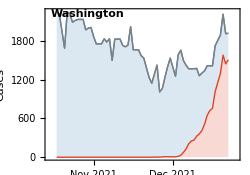

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

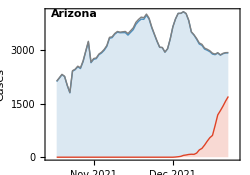
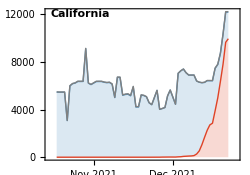
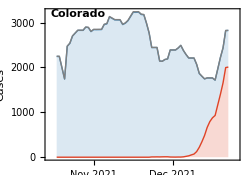
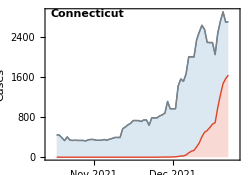
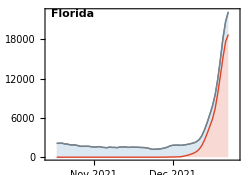
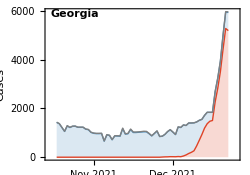
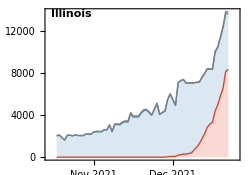
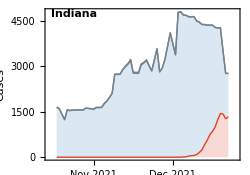
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=20000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png